```mathematica
(* IMPORT MODULES *)
ClearAll[m1,m2,m3]
loadDumpSaves=True;
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/parameters.nb"];
NotebookEvaluate["modules/golden_search.nb"];
If[loadDumpSaves,NotebookEvaluate["modules/load_dump_saves.nb"]];
SetDirectory[NotebookDirectory[]];
```

```mathematica
HamiltonianMin[J_,P_,FlavourSym_,γMax_,Λ_,S_,m1_,m2_,m3_,excited_,temperature_,wLeft_,wRight_,tolerance_,whichHamiltonian_:1,optimise_:True,omega_:1]:=Module[{},

ClearAll[case,proj,vCoulomb,vLinear,qhoSpect,kineticRho,kineticLam,wMin,hamiltonian,ham,sM,t1,t2,states,sM];
(* all different masses = 0, two equal masses = 1, all equal masses = 2 *)
case=If[m1==m2,1,0];
case=If[m1==m2==m3,2,case];
states=allStates[J,P,Λ,S,γMax];
sM=stateMatrix[J,P,Λ,S,γMax];

(* Calculate generalised transformation matrices *)
{t1time,t1}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,1]];
(*Print["Time taken to compute t1: ", ToString[t1time]];*)
{t2time,t2}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,2]];
(*Print["Time taken to compute t2: ", ToString[t2time]];*)

(* Obtain projector matrix *)
proj=projector[states,FlavourSym,case];

(* Required matrices for hamiltonian *)
vCoulomb=polynomialOperatorRho[sM,-1];(* 1/ρ matrix dimensionless *)
vLinear=polynomialOperatorRho[sM,1];(* ρ matrix dimensionless *)
qhoSpect=qhoSpectrum[sM];
kineticRho=polynomialOperatorRho[sM,2];
kineticLam=polynomialOperatorLambda[sM,2];

(* Choose which Hamiltonian to use (simple temp dependence = 1, Debye screened potential = 2) *)
If[whichHamiltonian==1,
(* Hamiltonian matrix *)
ham[ω_]:=Hb[ω,temperature,m1,m2,m3,proj],
ham[ω_]:=Hb2[ω,temperature,m1,m2,m3,proj]];

If[optimise,
(* Find minimum and errors*)
{minTime,{a,b,data}}=AbsoluteTiming[goldenSearch[ham,excited+1,wLeft,wRight,tolerance]];
(*Print["Time taken to find minimum: ", ToString[minTime],"s"];*)
wMin=(a+b)/2;
hamiltonian=ham[wMin],
hamiltonian=ham[omega]
];
(*eigvalMin=Eigenvalues[hamiltonian][[-excited-1]];
Print["{ω_min, E_min}: ",{Around[wMin,a-wMin],eigvalMin}];
Print["Number of basis functions (matrix size): ", Length[hamiltonian]]*)

(* Dump Saves, must only be saved if loadDumpSaves is True *)
If[loadDumpSaves,
DumpSave["modules/dumpSave/summationVariables.mx",summationVariables];
DumpSave["modules/dumpSave/talmi.mx",talmi];
DumpSave["modules/dumpSave/nineJ.mx",nineJ];
DumpSave["modules/dumpSave/rel.mx",rel];
DumpSave["modules/dumpSave/Rcoeff.mx",Rcoeff];
DumpSave["modules/dumpSave/Lcoeff.mx",Lcoeff];
];
hamiltonian
]
```

```mathematica
uq
```

0.315

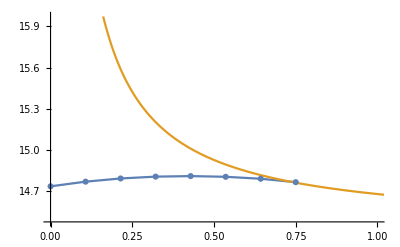

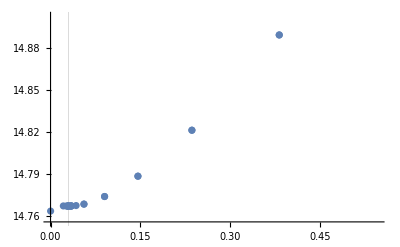

```mathematica
(* H1 TESTING *)
(**** !!!TUNABLE PARAMETERS!!! ****)
m1=bq;(* mass of quark 1 *)
m2=bq;(* mass of quark 2 *)
m3=bq;(* mass of quark 3 *)
Λ=1;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
S=1/2;(* Total spin *)
J=3/2;(* Total angular momentum J = Λ + S *)
P=-1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
FlavourSym=1;(* Flavour symmetry, 0=antisymmetric, 1=symmetric *)
γMax=6;(* Maximum energy of considered basis states (2n+l+2N+L) *)
excited=0;(* Choose excited state, 0 for ground state *)
temperature=0.0001; (* Temperature *)
wLeft=0.0001; (* golden search range start *)
wRight=1; (* golden search range end *)
tolerance=0.005;(* golden search tolerance *)
(**** !!! END OF TUNABLE PARAMETERS!!! ****)


plotData={};
start=0.0001;
end=0.75;
nSteps=7;
stepSize=(end-start)/nSteps;
temps=Table[t,{t,start,end,stepSize}];
For[tempStep=1,tempStep≤Length[temps],tempStep++,
temp=temps[[tempStep]];
ham=HamiltonianMin[J,P,FlavourSym,γMax,Λ,S,m1,m2,m3,excited,temp,wLeft,wRight,tolerance,whichHamiltonian=2,optimise=True];
eVal=Eigenvalues[ham][[-(excited+1)]];
AppendTo[plotData,{temp,eVal}]
]

boundary=Table[{μ,m1+m2+m3+3/2(coeffLinear/μ-Cqqq)-(2.02*10^-3)/(m1*m2*m3)},{μ,0.0001,2,0.001}];

ListPlot[{plotData,boundary},Joined->True,PlotMarkers->{Automatic,None},PlotRange->{{0,1},Automatic}]

ListPlot[data,GridLines->{{wMin},None}]

(*temperaturePlots=ListPlot[plots,
Joined->True,
PlotMarkers->Automatic,
PlotRange->{Automatic,{1.17,1.22}},
ScalingFunctions->{"Log",Automatic},
PlotLegends->{"T/T_C=0.9","T/T_C=0.99","T/T_C=0.999","T/T_C=0.9999","T/T_C=1"},
PlotTheme->"Scientific",
PlotLabel->"Λ_c(udc)",
FrameLabel->{"ω [GeV]","E [GeV]"},
LabelStyle->{FontFamily->"Arial",FontSize->14}
]*)
(*Export["plots/ch9_v1_udc_Jhalf_findingT.pdf",temperaturePlots,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]*)
```

```mathematica
InputForm[Round[plotData,10^-5]*1.]
```

{{0.0001, 14.73695}, {0.10723, 14.7709}, {0.21436, 14.79415}, {0.32149, 14.80746}, {0.42861, 14.81139}, {0.53574, 14.80628}, {0.64287, 14.79206}, {0.75, 14.76712}}

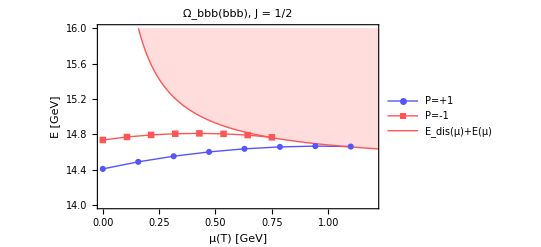

```mathematica
boundary=Table[{μ,bq+bq+bq+3/2(coeffLinear/μ-Cqqq)-(2.02*10^-3)/(bq*bq*bq)},{μ,0.0001,2,0.001}];
bbb1sP={{0.0001, 14.4099}, {0.15723, 14.4899}, {0.31436, 14.55343}, {0.47149, 14.60202}, 
{0.62861, 14.63682}, {0.78574, 14.65861}, {0.94287, 14.66769}, {1.1, 14.66284}};

bbb1sN={{0.0001, 14.73695}, {0.10723, 14.7709}, {0.21436, 14.79415}, {0.32149, 14.80746}, 
{0.42861, 14.81139}, {0.53574, 14.80628}, {0.64287, 14.79206}, {0.75, 14.76712}};

plot=ListPlot[{bbb1sP,bbb1sN,boundary},
Joined->True,
PlotMarkers->{Automatic,Automatic,None},
PlotRange->{{0,1.2},{14,16}},
PlotStyle->{Lighter[Blue],Lighter[Red],{Lighter[Red],Thin}},
PlotTheme->"Classic",
Frame->True,
Filling->{3->Top},
PlotLegends->{"P=+1","P=-1","E_dis(μ)+E(μ)"},
PlotLabel->"Ω_bbb(bbb), J = 1/2",
LabelStyle->{FontFamily->"Times",FontSize->14},
FrameLabel->{"μ(T) [GeV]","E [GeV]"}
]
```

```mathematica
Export["plots/ch7_v2_bbb_Jhalf_PvsN.pdf",plot,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch7_v2_bbb_Jhalf_PvsN.pdf

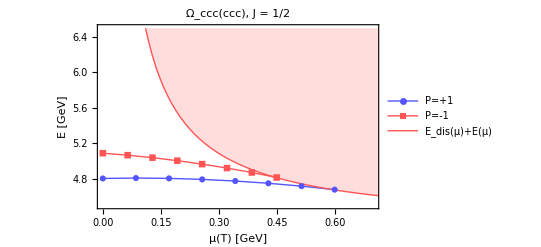

```mathematica
boundary=Table[{μ,cq+cq+cq+3/2(coeffLinear/μ-Cqqq)-(2.02*10^-3)/(cq*cq*cq)},{μ,0.0001,2,0.001}];
ccc1sP={{0.0001, 4.8021}, {0.0858, 4.80657}, {0.1715, 4.80282}, {0.2572, 4.79143}, {0.3429, 4.77286}, 
 {0.4286, 4.74745}, {0.5143, 4.71529}, {0.6, 4.67544}};

ccc1sN={{0.0001, 5.08753}, {0.06437, 5.06509}, {0.12864, 5.03683}, {0.19291, 5.00303}, 
 {0.25719, 4.96387}, {0.32146, 4.91944}, {0.38573, 4.86948}, {0.45, 4.81257}};

plot=ListPlot[{ccc1sP,ccc1sN,boundary},
Joined->True,
PlotMarkers->{Automatic,Automatic,None},
PlotRange->{{0,0.7},{4.5,6.5}},
PlotStyle->{Lighter[Blue],Lighter[Red],{Lighter[Red],Thin}},
PlotTheme->"Classic",
Frame->True,
Filling->{3->Top},
PlotLegends->{"P=+1","P=-1","E_dis(μ)+E(μ)"},
PlotLabel->"Ω_ccc(ccc), J = 1/2",
LabelStyle->{FontFamily->"Times",FontSize->14},
FrameLabel->{"μ(T) [GeV]","E [GeV]"}
]
```

```mathematica
Export["plots/ch7_v2_ccc_Jhalf_PvsN.pdf",plot,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch7_v2_ccc_Jhalf_PvsN.pdf

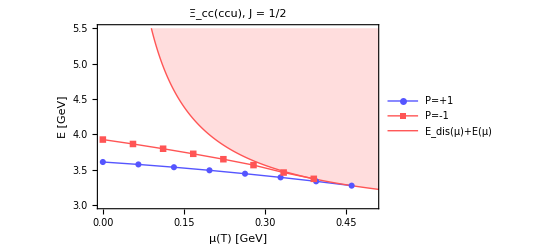

```mathematica
boundary=Table[{μ,cq+cq+uq+3/2(coeffLinear/μ-Cqqq)-(2.02*10^-3)/(cq*cq*uq)},{μ,0.0001,2,0.001}];
ccu1sP={{0.0001, 3.61001}, {0.0658, 3.57571}, {0.1315, 3.53642}, {0.1972, 3.49261}, 
{0.2629, 3.44466}, {0.3286, 3.3928}, {0.3943, 3.33693}, {0.46, 3.27595}};

ccu1sN={{0.0001, 3.9271}, {0.0558, 3.86475}, {0.1115, 3.79755}, {0.1672, 3.72573}, {0.2229, 3.64938}, 
 {0.2786, 3.56627}, {0.3343, 3.46119}, {0.39, 3.37228}};

plot=ListPlot[{ccu1sP,ccu1sN,boundary},
Joined->True,
PlotMarkers->{Automatic,Automatic,None},
PlotRange->{{0,0.5},{3,5.5}},
PlotStyle->{Lighter[Blue],Lighter[Red],{Lighter[Red],Thin}},
PlotTheme->"Classic",
Frame->True,
Filling->{3->Top},
PlotLegends->{"P=+1","P=-1","E_dis(μ)+E(μ)"},
PlotLabel->"Ξ_cc(ccu), J = 1/2",
LabelStyle->{FontFamily->"Times",FontSize->14},
FrameLabel->{"μ(T) [GeV]","E [GeV]"}
]
```

```mathematica
Export["plots/ch7_v2_ccu_Jhalf_PvsN.pdf",plot,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch7_v2_ccu_Jhalf_PvsN.pdf

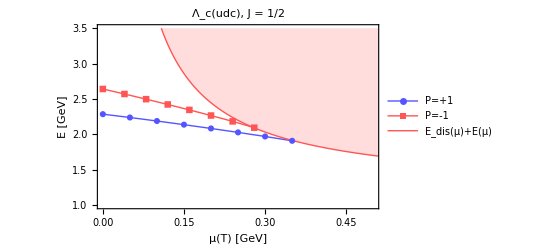

```mathematica
boundary=Table[{μ,uq+uq+cq+3/2(coeffLinear/μ-Cqqq)-(2.02*10^-3)/(uq*uq*cq)},{μ,0.0001,2,0.001}];
udc1sP={{0.0001,2.286008963332981},{0.05008571428571428,2.23885302060534},{0.10007142857142856,2.1892772635643944},{0.15005714285714283,2.137569195143546},{0.2000428571428571,2.0839397271546893},{0.2500285714285714,2.0284564314057563},{0.3000142857142857,1.9708574616557337},{0.3499999999999999,1.909769217910248}};
udc2sP={{0.0001,2.87618430677463},{0.040085714285714294,2.768188629994706},{0.08007142857142859,2.6589680687930524},{0.12005714285714288,2.5486154311371543},{0.16004285714285715,2.437123512745901},{0.20002857142857144,2.324397236339305},{0.24001428571428574,2.210318419900142},{0.28,2.092674536937741}};
udc3sP={{0.0001,3.101237817173267},{0.035800000000000005,2.970396466127442},{0.07150000000000001,2.8391609817194516},{0.1072,2.707887028642426},{0.1429,2.5768216265331865},{0.1786,2.4461564822642123},{0.2143,2.316657965919561},{0.25,2.19210315092349}};
udc1sN={{0.0001,2.641749803244962},{0.040085714285714294,2.570799991908392},{0.08007142857142859,2.4978546075079193},{0.12005714285714288,2.4229633635756875},{0.16004285714285715,2.3460362255262597},{0.20002857142857144,2.266720707035301},{0.24001428571428574,2.184060920377951},{0.28,2.0947444639987753}};

plot=ListPlot[{udc1sP,udc1sN,boundary},
Joined->True,
PlotMarkers->{Automatic,Automatic,None},
PlotRange->{{0,0.5},{1.0,3.5}},
PlotStyle->{Lighter[Blue],Lighter[Red],{Lighter[Red],Thin}},
PlotTheme->"Classic",
Frame->True,
Filling->{3->Top},
PlotLegends->{"P=+1","P=-1","E_dis(μ)+E(μ)"},
PlotLabel->"Λ_c(udc), J = 1/2",
LabelStyle->{FontFamily->"Times",FontSize->14},
FrameLabel->{"μ(T) [GeV]","E [GeV]"}
]
```

plots/ch7_v2_udc_Jhalf_PvsN.pdf

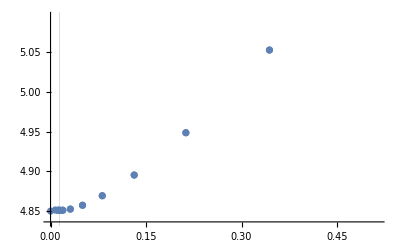

```mathematica
Export["plots/ch7_v2_udc_Jhalf_PvsN.pdf",plot,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

```mathematica
wMin
```

0.0525107

```mathematica
temps
```

{0.0001,0.0500857,0.100071,0.150057,0.200043,0.250029,0.300014,0.35}

```mathematica
data
```

{{0.0001,1.91526},{0.9,2.1268},{0.556269,2.00294},{0.343831,1.94487},{0.343831,1.94487},{0.212538,1.92089},{0.212538,1.92089},{0.131394,1.91323},{0.131394,1.91323},{0.0812439,1.91264},{0.0812439,1.91264},{0.0502497,1.91457},{0.100399,1.91239},{0.0812439,1.91264},{0.112238,1.91255},{0.100399,1.91239},{0.100399,1.91239},{0.0930827,1.91241},{0.104921,1.91243},{0.100399,1.91239},{0.100399,1.91239},{0.0976047,1.91239},{0.0976047,1.91239},{0.0958774,1.9124},{0.0986722,1.91239},{0.0976047,1.91239},{0.0993319,1.91239},{0.0986722,1.91239},{0.0986722,1.91239},{0.0982644,1.91239},{0.0982644,1.91239},{0.0980124,1.91239},{0.0984202,1.91239},{0.0982644,1.91239}}

```mathematica
(* WAVEFUNCTION AT ORIGIN *)
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
S=1/2;(* Total spin *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
FlavourSym=1;(* Flavour symmetry 1 = symmetric, 0 = antisymmetric *)
γMax=8;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
m1=cq;(* mass of quark 1 *)
m2=sq;(* mass of quark 2 *)
m3=uq;(* mass of quark 3 *)
excited=0;(* Choose excited state, 0 for ground state *)
temperature=0; (* Temperature *)
wLeft=0.0001; (* golden search range start *)
wRight=0.9; (* golden search range end *)
tolerance=0.0005;(* golden search tolerance *)
(**** !!! END OF TUNABLE PARAMETERS!!! ****)

hamMin=HamiltonianMin[J,P,FlavourSym,γMax,Λ,S,m1,m2,m3,excited,temperature,wLeft,wRight,tolerance];
eSys=Eigensystem[hamMin];
eVec=eSys[[2,-1]];
eVal=eSys[[1,-1]];
Print[eVal]
deltaMatrix3=delta3RhoMatrix[sM];
deltaMatrix1=Transpose[t1].deltaMatrix3.t1;
α[m1,m2,wMin]^3*eVec.(Transpose[proj].deltaMatrix3.proj).eVec*5.068^3*14.8/1.07176
α[m1,m2,wMin]^3*eVec.(Transpose[proj].deltaMatrix1.proj).eVec*5.068^3*14.8/1.07176
```

2.46535

26.2942

53.2018

t=0, ω=0.605807, E=2.46535

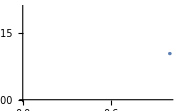

```mathematica
(* MEAN-SQUARED RADIUS *)
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
FlavourSym=1;(* Flavour symmetry 1 = symmetric, 0 = antisymmetric *)
γMax=8;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
S=1/2;(* Total spin *)
m1=uq;(* mass of quark 1 *)
m2=sq;(* mass of quark 2 *)
m3=cq;(* mass of quark 3 *)
excited=0;(* Choose excited state, 0 for ground state *)
temperature=0; (* Temperature *)
wLeft=0.0001; (* golden search range start *)
wRight=0.9; (* golden search range end *)
tolerance=0.0005;(* golden search tolerance *)
(**** !!! END OF TUNABLE PARAMETERS!!! ****)


expValsData={};
For[temperature=0,temperature≤0,temperature+=1,

hamMin=HamiltonianMin[J,P,FlavourSym,γMax,Λ,S,m1,m2,m3,excited,temperature,wLeft,wRight,tolerance];

system=Eigensystem[hamMin];

eval=system[[1,-1-excited]];
evec=system[[2,-1-excited]];

Print["t=",temperature,", ω=",wMin,", E=",eval];

(* Find expectation values of <λ^2> *)
lamSqrd12=1/β[m1,m2,m3,wMin]^2 kineticLam;
lamSqrd23=1/β1[m1,m2,m3,wMin]^2 Transpose[t1].kineticLam.t1;
lamSqrd31=1/β2[m1,m2,m3,wMin]^2 Transpose[t2].kineticLam.t2;
lams={lamSqrd12,lamSqrd23,lamSqrd31};
expValsLam=Table[evec.(Transpose[proj].lams[[i]].proj).evec,{i,1,3}];

(* Mean mass-square radius using exact method *)
expVals=expValsLam/5.068^2;
λ3Squared=expVals[[1]];
λ1Squared=expVals[[2]];
λ2Squared=expVals[[3]];
M=m1+m2+m3;
term1=(m1(m2+m3)^2)/M^3 λ1Squared;
term2=(m2(m1+m3)^2)/M^3 λ2Squared;
term3=(m3(m1+m2)^2)/M^3 λ3Squared;
RmSquared=term1+term2+term3;

AppendTo[expValsData,RmSquared]

(*Print[ListPlot[Sort[data],Joined->True,PlotMarkers->Automatic,ImageSize->Small]]*)
]

ListPlot[expValsData]
```

```mathematica
test={{1,2,0,0,0,0},{3,4,0,0,0,0},{0,0,9,10,0,0},{0,0,11,12,0,0},{0,0,0,0,5,6},{0,0,0,0,7,8}};
test//MatrixForm
```

(1 | 2 | 0 | 0 | 0 | 0
3 | 4 | 0 | 0 | 0 | 0
0 | 0 | 9 | 10 | 0 | 0
0 | 0 | 11 | 12 | 0 | 0
0 | 0 | 0 | 0 | 5 | 6
0 | 0 | 0 | 0 | 7 | 8)

```mathematica
Eigenvalues[test]*1.
```

{21.0948,13.1521,5.37228,-0.372281,-0.152067,-0.0948101}

```mathematica
Eigenvalues[{{1,2},{3,4}}]*1.
```

{5.37228,-0.372281}

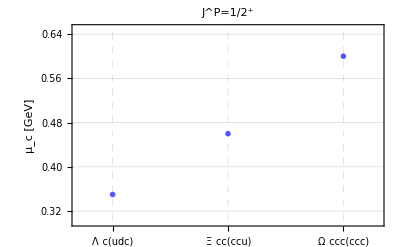

```mathematica
plot=ListPlot[{{1,0.35},{2,0.46},{3,0.6}},
PlotTheme->"Classic",
Joined->False,
GridLines->{{1,2,3},Automatic},
GridLinesStyle->Directive[Gray, Dashed,Opacity[0.3]],
PlotMarkers->{"x",Large},
Frame->True,
PlotStyle->{Lighter[Blue]},
FrameLabel->{"","μ_c [GeV]"},
PlotLabel->"J^P=1/2^+",
FrameTicks->{Automatic,{{{1,"Λ_c(udc)"},{2,"Ξ_cc(ccu)"},{3,"Ω_ccc(ccc)"}},None}},
PlotRange->{{0.7,3.3},{0.3,0.65}},
LabelStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
Export["plots/ch7_v2_crit_temp_charms.pdf",plot,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch7_v2_crit_temp_charms.pdf

```mathematica
6
```